```mathematica
Subscript[w, 11]=RandomReal[1]
```

0.91959

```mathematica
Subscript[w, 12]=RandomReal[1]
```

0.700534

```mathematica
Subscript[w, 24]=RandomReal[1]
```

0.81391

```mathematica
Subscript[w, 23]=RandomReal[1]
```

0.00378332

```mathematica
Subscript[v, 12]=RandomReal[1]
```

0.805398

```mathematica
Subscript[v, 13]=RandomReal[1]
```

0.949069

```mathematica
Subscript[v, 23]=RandomReal[1]
```

0.766521

```mathematica
Subscript[v, 33]= RandomReal[1]
```

0.284567

```mathematica
Subscript[v, 43]= RandomReal[1]
```

0.885745

```mathematica
Subscript[h, 1]=RandomReal[{0.1,1}]
```

0.624039

```mathematica
Subscript[h, 2]=RandomReal[{0.1,1}]
```

0.216578

```mathematica
Subscript[h, 3]=RandomReal[{0.1,1}]
```

0.675626

```mathematica
Subscript[h, 4]=RandomReal[{0.1,1}]
```

0.780445

```mathematica
Subscript[g, 1][Subscript[c, 1]]= 0
```

0

```mathematica
Subscript[g, 2][Subscript[c, 2]]= Subscript[v, 12]*Subscript[c, 1][t]
```

0.805398 c_1[t]

```mathematica
Subscript[g, 3][Subscript[c, 3]]=(Subscript[v, 13]*Subscript[c, 1][t])+(Subscript[v, 23]*Subscript[c, 2][t])+(Subscript[v, 33]*Subscript[c, 3][t])+(Subscript[v, 43]*Subscript[c, 4][t])
```

0.949069 c_1[t]+0.766521 c_2[t]+0.284567 c_3[t]+0.885745 c_4[t]

```mathematica
Subscript[r, 1][Subscript[c, 1]]=Subscript[c, 1][t]/(Subscript[h, 1]+Subscript[c, 1][t])
```

c_1[t]/(0.624039+c_1[t])

```mathematica
Subscript[r, 2][Subscript[c, 2]]=Subscript[c, 2][t]/(Subscript[h, 2]+Subscript[c, 2][t])
```

c_2[t]/(0.216578+c_2[t])

```mathematica
Subscript[r, 3][Subscript[c, 3]]=Subscript[c, 3][t]/(Subscript[h, 3]+Subscript[c, 3][t])
```

c_3[t]/(0.675626+c_3[t])

```mathematica
Subscript[r, 4][Subscript[c, 4]]=Subscript[c, 4][t]/(Subscript[h, 4]+Subscript[c, 4][t])
```

c_4[t]/(0.780445+c_4[t])

```mathematica
Subscript[μ, 1]= RandomReal[{0.01,0.1}]
```

0.0895828

```mathematica
Subscript[μ, 2]= RandomReal[{0.01,0.1}]
```

0.073113

```mathematica
Subscript[μ, 3]= RandomReal[{0.01,0.1}]
```

0.0145681

```mathematica
Subscript[μ, 4]= RandomReal[{0.01,0.1}]
```

0.0647443

```mathematica
Subscript[δ, 1]=RandomReal[{0.01,0.1}]
```

0.0830556

```mathematica
Subscript[δ, 2]=RandomReal[{0.01,0.1}]
```

0.0148836

```mathematica
Subscript[δ, 3]=RandomReal[{0.01,0.1}]
```

0.0161064

```mathematica
Subscript[s, 1]=RandomReal[5]
```

4.80166

```mathematica
Subscript[s, 2]=RandomReal[5]
```

0.420819

```mathematica
Subscript[s, 3]=RandomReal[5]
```

2.93299

```mathematica
Subscript[s, 4]=RandomReal[5]
```

2.16916

```mathematica
sim= NDSolve[{Subscript[x, 1]'[t]==  Subscript[x, 1][t](Subscript[g, 1][Subscript[c, 1]]+Subscript[δ, 1]),Subscript[x, 2]'[t]==  Subscript[x, 2][t](Subscript[g, 2][Subscript[c, 2]]+Subscript[δ, 2]),Subscript[x, 3]'[t]==  Subscript[x, 3][t](Subscript[g, 3][Subscript[c, 3]]+Subscript[δ, 3]),Subscript[c, 1]'[t]== Subscript[s, 1]+((Subscript[w, 11]*Subscript[x, 1][t])*Subscript[r, 1][Subscript[c, 1]])-(((Subscript[v, 12]*Subscript[x, 2][t])+(Subscript[v, 13]*Subscript[x, 3][t]))*Subscript[r, 1][Subscript[c, 1]])-(Subscript[μ, 1]*Subscript[c, 1][t]),Subscript[c, 2]'[t]== Subscript[s, 2]+((Subscript[w, 12]*Subscript[x, 1][t])*Subscript[r, 2][Subscript[c, 2]])-((Subscript[v, 23]*Subscript[x, 3][t])*Subscript[r, 2][Subscript[c, 2]])-(Subscript[μ, 2]*Subscript[c, 2][t]),Subscript[c, 3]'[t]== Subscript[s, 3]+((Subscript[w, 23]*Subscript[x, 2][t])*Subscript[r, 3][Subscript[c, 3]])-((Subscript[v, 33]*Subscript[x, 3][t])*Subscript[r, 3][Subscript[c, 3]])-(Subscript[μ, 3]*Subscript[c, 3][t]),Subscript[c, 4]'[t]== Subscript[s, 4]+((Subscript[w, 24]*Subscript[x, 2][t])*Subscript[r, 4][Subscript[c, 4]])-((Subscript[v, 43]*Subscript[x, 3][t])*Subscript[r, 4][Subscript[c, 4]])-(Subscript[μ, 4]*Subscript[c, 4][t]),Subscript[x, 1][0]== 2.234,Subscript[x, 2][0]== 2.763,Subscript[x, 3][0]== 3.432,Subscript[c, 1][0]== Subscript[s, 1],Subscript[c, 2][0]== Subscript[s, 2],Subscript[c, 3][0]== Subscript[s, 3],Subscript[c, 4][0]== Subscript[s, 4]},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4]},{t,0,100}];
```

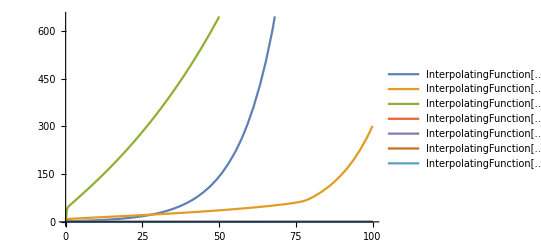

```mathematica
Plot[Evaluate[{Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t],Subscript[c, 1][t],Subscript[c, 2][t],Subscript[c, 3][t],Subscript[c, 4][t]}/.sim],{t,0,100},PlotLegends->"Expressions"]
```